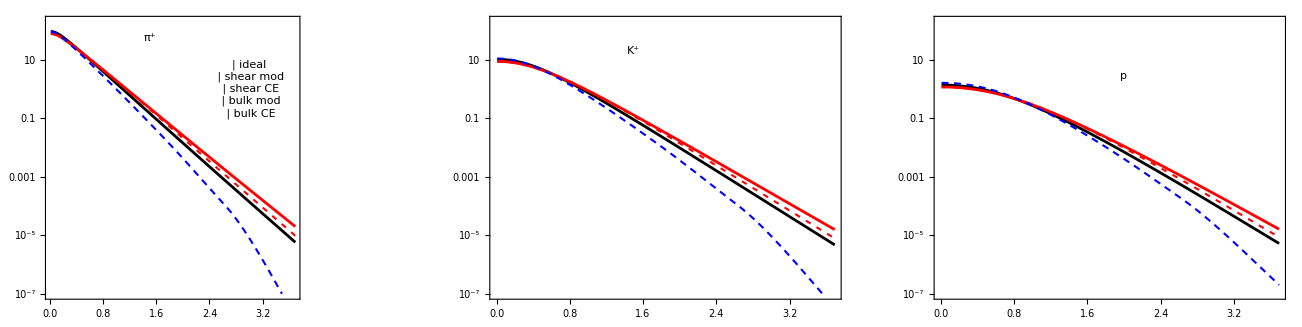
-Graphics-p_T (GeV)

modified_spectra.pdf

```mathematica
SetDirectory@NotebookDirectory[];
style={Directive[Black,AbsoluteThickness[2]],
Directive[Red,AbsoluteThickness[2]],Directive[Red,AbsoluteThickness[1.5],AbsoluteDashing[{4,5}]],Directive[Blue,AbsoluteThickness[2]],Directive[Blue,AbsoluteThickness[1.5],AbsoluteDashing[{5,4}]]};

pion = {idealπ,shearmodπ,shearCEπ,0bulkmodπ,bulkCEπ};
kaon= {idealK,shearmodK,shearCEK,0bulkmodK,bulkCEK};
proton={idealp,shearmodp,shearCEp,0bulkmodp,bulkCEp};

vT = 0.6;uT=vT/Sqrt[1-vT^2];ut=Sqrt[1+uT^2];
LogPlot[1/(Exp[ut*Sqrt[pT^2+(0.14)^2]-uT*pT]-1),{pT,0,3}];

legenddf=Panel[Grid[{{Graphics[{style[[1]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["ideal",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{style[[2]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["shear mod",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{style[[3]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["shear CE",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{style[[4]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["bulk mod",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{style[[5]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["bulk CE",FontSize->14,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];

legendπ=Panel[Grid[{{Style["π^+",FontSize->18,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];
legendK=Panel[Grid[{{Style["K^+",FontSize->18,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];
legendp=Panel[Grid[{{Style["p",FontSize->18,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];


spectra=Panel[GraphicsGrid[{{ListLogPlot[pion,PlotRange->{{0,3.69},{10^-7,200}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->400,AspectRatio->0.75,PlotStyle->style,Epilog->{Inset[legenddf,{3.0,.0}],Inset[legendπ,{1.5,4}]}],
ListLogPlot[kaon,PlotRange->{{0,3.69},{10^-7,200}},Frame->True,FrameStyle->Black,RotateLabel->True,Joined->True,BaseStyle->{FontSize->12},InterpolationOrder->2,ImageSize->400,AspectRatio->0.75,PlotStyle->style,Epilog->{Inset[legendK,{1.5,3}]}],
ListLogPlot[proton,PlotRange->{{0,3.69},{10^-7,200}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->400,AspectRatio->0.75,PlotStyle->style,Epilog->{Inset[legendp,{2.0,1}]}]}},PlotLabel->Style["dN/p_T|_(y, SubscriptBox[ϕ, p] = 0)",FontSize->24,FontFamily->"Calibri",Black]],Style["p_T (GeV)",FontFamily->"Calibri",FontSize->16],{{Bottom,Center}},Appearance->"Frameless",ImageSize->{1300,320},FrameMargins->0,Background->White]
Export["modified_spectra.pdf",spectra]
```

### Pion

```mathematica
idealπ=
{{7.17752430*10^-03,9.35156423*10^+01},
{3.78993630*10^-02,9.15949661*10^+01},
{9.35073360*10^-02,8.25350264*10^+01},
{1.74611500*10^-01,6.35868130*10^+01},
{2.82124830*10^-01,4.11410549*10^+01},
{4.17333600*10^-01,2.26928018*10^+01},
{5.81993540*10^-01,1.07288012*10^+01},
{7.78479140*10^-01,4.32043015*10^+00},
{1.01002170*10^+00,1.46413494*10^+00},
{1.28110830*10^+00,4.10560086*10^-01},
{1.59819070*10^+00,9.28980094*10^-02},
{1.97106870*10^+00,1.62893980*10^-02},
{2.41596300*10^+00,2.06330372*10^-03},
{2.96389860*10^+00,1.64431995*10^-04},
{3.69431420*10^+00,5.76305272*10^-06}};


shearCEπ=
{{7.17752430*10^-03,7.72457127*10^+01},
{3.78993630*10^-02,7.59870197*10^+01},
{9.35073360*10^-02,6.98879362*10^+01},
{1.74611500*10^-01,5.62031938*10^+01},
{2.82124830*10^-01,3.84784604*10^+01},
{4.17333600*10^-01,2.26412125*10^+01},
{5.81993540*10^-01,1.14965195*10^+01},
{7.78479140*10^-01,4.98270306*10^+00},
{1.01002170*10^+00,1.80935986*10^+00},
{1.28110830*10^+00,5.39326568*10^-01},
{1.59819070*10^+00,1.28690977*10^-01},
{1.97106870*10^+00,2.36529794*10^-02},
{2.41596300*10^+00,3.13383614*10^-03},
{2.96389860*10^+00,2.61582076*10^-04},
{3.69431420*10^+00,9.64342196*10^-06}};


shearmodπ ={{7.17752430*10^-03,7.92280358*10^+01},{3.78993630*10^-02,7.78204526*10^+01},{9.35073360*10^-02,7.10895738*10^+01},{1.74611500*10^-01,5.64625883*10^+01},{2.82124830*10^-01,3.81524233*10^+01},{4.17333600*10^-01,2.22073232*10^+01},{5.81993540*10^-01,1.12112374*10^+01},{7.78479140*10^-01,4.88575433*10^+00},{1.01002170*10^+00,1.81700017*10^+00},{1.28110830*10^+00,5.67198838*10^-01},{1.59819070*10^+00,1.45100852*10^-01},{1.97106870*10^+00,2.93037327*10^-02},{2.41596300*10^+00,4.38295697*10^-03},{2.96389860*10^+00,4.28459872*10^-04},{3.69431420*10^+00,1.97800423*10^-05}};

bulkmodπ=
{{7.17752430*10^-03 ,1.29010207*10^+02},
{3.78993630*10^-02 ,1.34033009*10^+02},
{9.35073360*10^-02 ,1.52151379*10^+02},
{1.74611500*10^-01 ,1.68479521*10^+02},
{2.82124830*10^-01 ,1.58521696*10^+02},
{4.17333600*10^-01 ,1.26712631*10^+02},
{5.81993540*10^-01 ,8.95176933*10^+01},
{7.78479140*10^-01 ,5.71668186*10^+01},
{1.01002170*10^+00 ,3.31174158*10^+01},
{1.28110830*10^+00 ,1.72424039*10^+01},
{1.59819070*10^+00 ,7.90507123*10^+00},
{1.97106870*10^+00 ,3.08248688*10^+00},
{2.41596300*10^+00 ,9.60180795*10^-01},
{2.96389860*10^+00 ,2.08472479*10^-01},
{3.69431420*10^+00 ,2.02682086*10^-02}};



bulkCEπ=
{{7.17752430*10^-03,9.17694563*10^+01},{3.78993630*10^-02,8.96294757*10^+01},{9.35073360*10^-02,7.95686198*10^+01},{1.74611500*10^-01,5.91963760*10^+01},{2.82124830*10^-01,3.64709164*10^+01},{4.17333600*10^-01,1.89581803*10^+01},{5.81993540*10^-01,8.32609693*10^+00},{7.78479140*10^-01,3.05079934*10^+00},{1.01002170*10^+00,9.15065053*10^-01},{1.28110830*10^+00,2.18285284*10^-01},{1.59819070*10^+00,3.95261677*10^-02},{1.97106870*10^+00,4.99730400*10^-03},{2.41596300*10^+00,3.72324777*10^-04},{2.96389860*10^+00,1.06509990*10^-05},{3.69431420*10^+00,1.55539952*10^-08}};
```

### Kaon

```mathematica
idealK={{7.17752430*10^-03,1.03984107*10^+01},{3.78993630*10^-02,1.03500674*10^+01},{9.35073360*10^-02,1.00983642*10^+01},{1.74611500*10^-01,9.38392066*10^+00},{2.82124830*10^-01,7.96107656*10^+00},{4.17333600*10^-01,5.86851145*10^+00},{5.81993540*10^-01,3.60505288*10^+00},{7.78479140*10^-01,1.80144275*10^+00},{1.01002170*10^+00,7.24151383*10^-01},{1.28110830*10^+00,2.32080930*10^-01},{1.59819070*10^+00,5.83259648*10^-02},{1.97106870*10^+00,1.11186433*10^-02},{2.41596300*10^+00,1.50713106*10^-03},{2.96389860*10^+00,1.27101465*10^-04},{3.69431420*10^+00,4.68314070*10^-06}};

shearCEK={{7.17752430*10^-03,8.69380889*10^+00},{3.78993630*10^-02,8.66177598*10^+00},{9.35073360*10^-02,8.49435850*10^+00},{1.74611500*10^-01,8.01272278*10^+00},{2.82124830*10^-01,7.02034440*10^+00},{4.17333600*10^-01,5.46315241*10^+00},{5.81993540*10^-01,3.61267974*10^+00},{7.78479140*10^-01,1.96543963*10^+00},{1.01002170*10^+00,8.58574955*10^-01},{1.28110830*10^+00,2.95886006*10^-01},{1.59819070*10^+00,7.90818986*10^-02},{1.97106870*10^+00,1.59006934*10^-02},{2.41596300*10^+00,2.26533990*10^-03},{2.96389860*10^+00,2.00770935*10^-04},{3.69431420*10^+00,7.80022390*10^-06}};

shearmodK={{7.17752430*10^-03,8.86679979*10^+00},{3.78993630*10^-02,8.83114503*10^+00},{9.35073360*10^-02,8.64518339*10^+00},{1.74611500*10^-01,8.11411204*10^+00},{2.82124830*10^-01,7.03874746*10^+00},{4.17333600*10^-01,5.40101376*10^+00},{5.81993540*10^-01,3.52481674*10^+00},{7.78479140*10^-01,1.90780239*10^+00},{1.01002170*10^+00,8.44999728*10^-01},{1.28110830*10^+00,3.03081620*10^-01},{1.59819070*10^+00,8.66064776*10^-02},{1.97106870*10^+00,1.91213429*10^-02},{2.41596300*10^+00,3.07683929*10^-03},{2.96389860*10^+00,3.19885835*10^-04},{3.69431420*10^+00,1.56013399*10^-05}};



bulkmodK={{7.17752430*10^-03, 2.07980772*10^+01},
{3.78993630*10^-02, 2.08507216*10^+01},
{9.35073360*10^-02, 2.11152792*10^+01},
{1.74611500*10^-01, 2.17816726*10^+01},
{2.82124830*10^-01, 2.27464187*10^+01},
{4.17333600*10^-01, 2.32192890*10^+01},
{5.81993540*10^-01, 2.19790959*10^+01},
{7.78479140*10^-01, 1.84826724*10^+01},
{1.01002170*10^+00, 1.34998974*10^+01},
{1.28110830*10^+00, 8.47510896*10^+00},
{1.59819070*10^+00, 4.51984956*10^+00},
{1.97106870*10^+00, 1.99949607*10^+00},
{2.41596300*10^+00, 6.97513010*10^-01},
{2.96389860*10^+00, 1.70559161*10^-01},
{3.69431420*10^+00, 2.00417477*10^-02}};

bulkCEK={{7.17752430*10^-03,1.10806210*10^+01},{3.78993630*10^-02,1.10247022*10^+01},{9.35073360*10^-02,1.07329545*10^+01},{1.74611500*10^-01,9.90125689*10^+00},{2.82124830*10^-01,8.24412146*10^+00},{4.17333600*10^-01,5.84850794*10^+00},{5.81993540*10^-01,3.37162173*10^+00},{7.78479140*10^-01,1.53860137*10^+00},{1.01002170*10^+00,5.48192537*10^-01},{1.28110830*10^+00,1.50121870*10^-01},{1.59819070*10^+00,3.05534129*10^-02},{1.97106870*10^+00,4.30500157*10^-03},{2.41596300*10^+00,3.60984743*10^-04},{2.96389860*10^+00,1.22604805*10^-05},{3.69431420*10^+00,3.23305215*10^-08}};
```

### Proton

```mathematica
idealp={{7.17752430*10^-03,1.37742446*10^+00},{3.78993630*10^-02,1.37438827*10^+00},{9.35073360*10^-02,1.35843844*10^+00},{1.74611500*10^-01,1.31170964*10^+00},{2.82124830*10^-01,1.21057590*10^+00},{4.17333600*10^-01,1.03429432*10^+00},{5.81993540*10^-01,7.84664880*10^-01},{7.78479140*10^-01,5.04853379*10^-01},{1.01002170*10^+00,2.64248021*10^-01},{1.28110830*10^+00,1.08836958*10^-01},{1.59819070*10^+00,3.42555411*10^-02},{1.97106870*10^+00,7.94272286*10^-03},{2.41596300*10^+00,1.27460620*10^-03},{2.96389860*10^+00,1.24506112*10^-04},{3.69431420*10^+00,5.24430536*10^-06}};

shearCEp={{7.17752430*10^-03,1.16695695*10^+00},{3.78993630*10^-02,1.16490535*10^+00},{9.35073360*10^-02,1.15411071*10^+00},{1.74611500*10^-01,1.12231574*10^+00},{2.82124830*10^-01,1.05252051*10^+00},{4.17333600*10^-01,9.27035991*10^-01},{5.81993540*10^-01,7.39043113*10^-01},{7.78479140*10^-01,5.09777675*10^-01},{1.01002170*10^+00,2.90091795*10^-01},{1.28110830*10^+00,1.29953010*10^-01},{1.59819070*10^+00,4.41082201*10^-02},{1.97106870*10^+00,1.09309918*10^-02},{2.41596300*10^+00,1.86359012*10^-03},{2.96389860*10^+00,1.92892949*10^-04},{3.69431420*10^+00,8.62261527*10^-06}};



shearmodp={{7.17752430*10^-03,1.18499493*10^+00},{3.78993630*10^-02,1.18272614*10^+00},{9.35073360*10^-02,1.17079874*10^+00},{1.74611500*10^-01,1.13577782*10^+00},{2.82124830*10^-01,1.05952162*10^+00},{4.17333600*10^-01,9.24661577*10^-01},{5.81993540*10^-01,7.27985679*10^-01},{7.78479140*10^-01,4.96151345*10^-01},{1.01002170*10^+00,2.81459179*10^-01},{1.28110830*10^+00,1.28564926*10^-01},{1.59819070*10^+00,4.58951676*10^-02},{1.97106870*10^+00,1.23547389*10^-02},{2.41596300*10^+00,2.36689440*10^-03},{2.96389860*10^+00,2.87226021*10^-04},{3.69431420*10^+00,1.61644724*10^-05}};

bulkmodp={{7.17752430*10^-03, 3.04401898*10^+00},
{3.78993630*10^-02, 3.04631570*10^+00},
{9.35073360*10^-02, 3.05839632*10^+00},
{1.74611500*10^-01, 3.09391003*10^+00},
{2.82124830*10^-01, 3.17081233*10^+00},
{4.17333600*10^-01, 3.30126358*10^+00},
{5.81993540*10^-01, 3.46169367*10^+00},
{7.78479140*10^-01, 3.54745898*10^+00},
{1.01002170*10^+00, 3.38448742*10^+00},
{1.28110830*10^+00, 2.85682350*10^+00},
{1.59819070*10^+00, 2.04483461*10^+00},
{1.97106870*10^+00, 1.19532674*10^+00},
{2.41596300*10^+00, 5.43763692*10^-01},
{2.96389860*10^+00, 1.75147284*10^-01},
{3.69431420*10^+00, 3.02697692*10^-02}};


bulkCEp={{7.17752430*10^-03,1.63262880*10^+00},{3.78993630*10^-02,1.62893244*10^+00},{9.35073360*10^-02,1.60947172*10^+00},{1.74611500*10^-01,1.55208093*10^+00},{2.82124830*10^-01,1.42639346*10^+00},{4.17333600*10^-01,1.20465089*10^+00},{5.81993540*10^-01,8.90219145*10^-01},{7.78479140*10^-01,5.45232709*10^-01},{1.01002170*10^+00,2.63531908*10^-01},{1.28110830*10^+00,9.65423682*10^-02},{1.59819070*10^+00,2.57577397*10^-02},{1.97106870*10^+00,4.71802455*10^-03},{2.41596300*10^+00,5.26158196*10^-04},{2.96389860*10^+00,2.65809392*10^-05},{3.69431420*10^+00,1.99751063*10^-07}};
```